```mathematica
f0[c_,cm_]:=-(A/2)(c-cm)^2+B/4(c-cm)^4+cα/4(c-cα)^4+cβ/4(c-cβ)^4
```

```mathematica
f0[c_]:=f0[c,cm];
```

```mathematica
D[f0[c],c]
```

-A (c-cm)+B (c-cm)^3+(c-cα)^3 cα+(c-cβ)^3 cβ

```mathematica
2.0/(0.05-0.5*(0.05+0.95))^2
```

9.87654

```mathematica
2/(0.95-0.05)
```

2.22222

```mathematica
√3.0
```

1.73205

```mathematica
Collect[Collect[Expand[-A (c-cm)+B (c-cm)^3+(c-cα)^3 cα+(c-cβ)^3 cβ],c]/.{c->cg,c^2->2cg c,c^3->3 cg c^2},cg]
```

A cm-B cm^3-cα^4-cβ^4+cg (-A+3 B cm^2+3 cα^3+3 cβ^3+3 c^2 (B+cα+cβ)+2 c (-3 B cm-3 cα^2-3 cβ^2))

```mathematica
Collect[D[Out[32], cg],c]
```

-A+3 B cm^2+3 cα^3+3 cβ^3+3 c^2 (B+cα+cβ)+2 c (-3 B cm-3 cα^2-3 cβ^2)

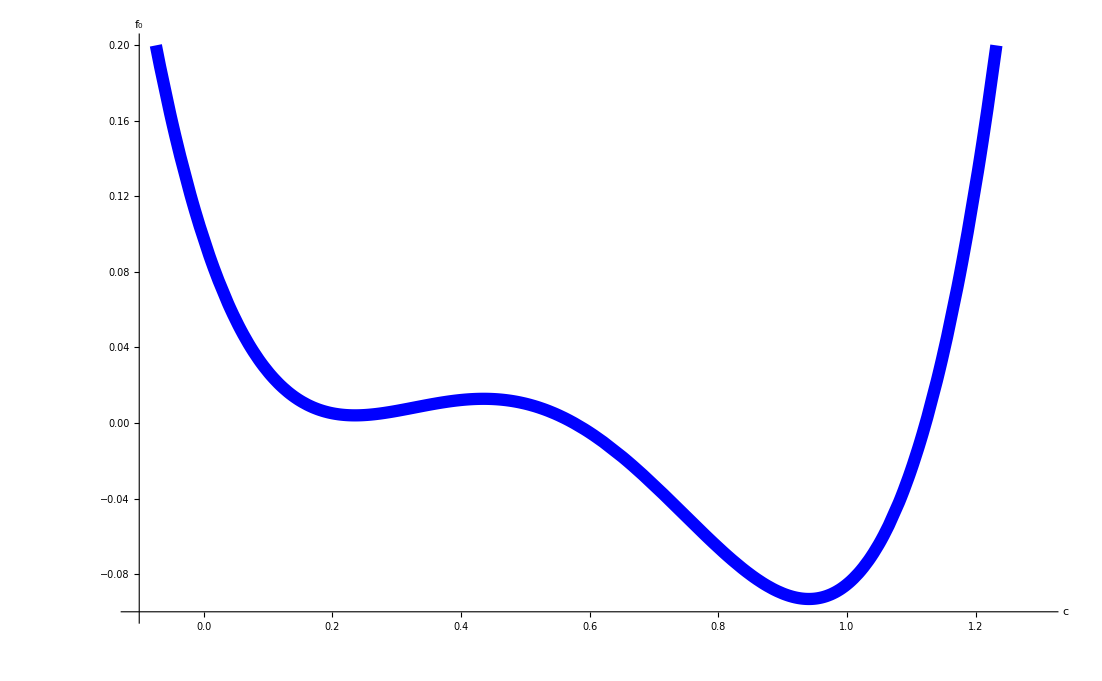

```mathematica
Plot[-2/2(c-0.5)^2+9.8765/4(c-0.5)^4+0.05/4(c-0.05)^4+0.95/4(c-0.95)^4,{c,-1,2},PlotRange->{{-0.1,1.3},{-0.1,0.2}},AxesOrigin->{-0.1,-0.1},TicksStyle->Directive[Black,25],AxesLabel->{Style["c",FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->30],Style["f_0",FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->30]},PlotStyle->Directive[Blue,Thickness[0.008]]]
```

```mathematica
√233.
```

15.2643

```mathematica
√239.
```

15.4596

```mathematica
f1[c_]:=-A/2(c-cm)^2+B/4(c-cm)^4+Da/4(c-ca)^4+Db/4(c-cb)^4
```

```mathematica
f2[c_,η_]:=-γ/2(c-ca)^2 η^2+β/4 η^4
```

```mathematica
f3[ηi_,ηj_]:=ϵ/2 ηi^2 ηj^2
```

```mathematica
D[f1[c],c]
```

-A (c-cm)+B (c-cm)^3+(c-ca)^3 Da+(c-cb)^3 Db

```mathematica
ηvec = {η1,η2,η3,η4,η5,η6,η7,η8,η9,η10};
```

```mathematica
Simplify[Sum[D[f2[c,ηvec[[j]]],c],{j,1,10}]]
```

-(c-ca) γ (η1^2+η10^2+η2^2+η3^2+η4^2+η5^2+η6^2+η7^2+η8^2+η9^2)

```mathematica
γ = 2/(0.05-0.95)^2
```

2.46914

```mathematica
Table[√(23.+i),{i,1,10,1}]
```

{4.89898,5.,5.09902,5.19615,5.2915,5.38516,5.47723,5.56776,5.65685,5.74456}

```mathematica
Table[√(149.+i),{i,1,10,1}]
```

{12.2474,12.2882,12.3288,12.3693,12.4097,12.4499,12.49,12.53,12.5698,12.6095}

```mathematica
Solve[320/x==15.,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→21.3333}}